# Strava segment analysis

```mathematica
raw= Import[ToFileName[NotebookDirectory[] <> "/data/","segment1.csv"]];
```

```mathematica
colnames = Flatten[Take[raw,1]]
```

{Date,Speed_Kmh,Power_W,Time_M_S}

```mathematica
data = Drop[raw,1];
dates = Map[DateObject,data[[All,1]]]  ;
```

```mathematica
durations = Map[Function[s,With[{l=StringSplit[s,":"]},ToExpression[l⟦1⟧] 60+ToExpression[l⟦2⟧]]],data[[All,4]]];
```

List of {date,duration} paris:

```mathematica
dd=Transpose[{dates, durations}];
```

Plot of all ride durations:

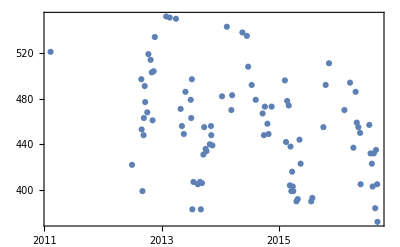

```mathematica
DateListPlot[dd,Joined->False]
```

Histogram of all ride durations 2011-2016:

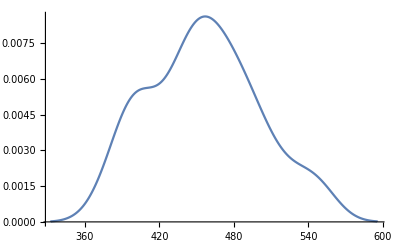

```mathematica
SmoothHistogram[durations]
```

```mathematica
dist=FindDistribution[durations]
```

FindDistribution::conenf: The data will be treated as continuous. Use the option TargetFunctions->Discrete otherwise.

MixtureDistribution[{0.63507,0.36493},{UniformDistribution[{372.045,551.874}],NormalDistribution[454.64,26.3779]}]

So the distribution is a mixture of uniform and normal distributions. Let us examine it more closely:

```mathematica
distpdf=PDF[dist,x]
```

Piecewise[{{0.+0.00551923 ⅇ^(-0.000718601 (-454.64+x)^2), x>551.874||x<372.045}, {0.00353152+0.00551923 ⅇ^(-0.000718601 (-454.64+x)^2), True}}]

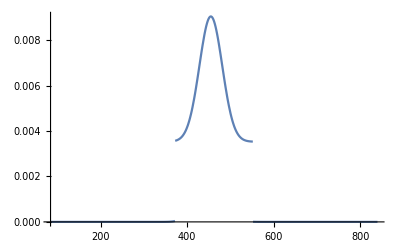

```mathematica
Plot[distpdf,{x,84.31804732849685,839.6000220767548}]
```

But we need to clear data little more:

1. I know that I started riding regularly in second half of 2012, so data before that is some kind of error
2. There is seems to be a seasonal component which could be explained that I usually ride more cautiously on wet road. We will ignore it for now.
3. Finally, it looks like the results change as I get more in shape, so we will need to look at it by year.